```mathematica
NormalizeData[symbol_,start_,end_]:=FinancialData[symbol,{start,end}]//Transpose@{#[[All,1]],#[[All,2]]/First@#[[All,2]]}&
GetData[symbol_,start_,end_]:=FinancialData["QQQ","OHLCV",{start,end}]
HedgeChart[stock_,inverse_,start_,end_]:=Module[{s1,s2,portfolio},
s1=NormalizeData[stock,start,end];
s2=NormalizeData[inverse,start,end];
portfolio=Transpose@{s2[[All,1]],Mean/@Transpose@{s1[[All,2]],s2[[All,2]]}};
DateListPlot[{s1,s2,portfolio},PlotLegends->{stock,inverse,stock<>" & "<>inverse},PlotTheme->"Detailed",ImageSize->Large,BaseStyle->{FontSize->20},PlotRange->All]
]
PortfolioChart[stocks_,start_,end_]:=Module[{s,portfolio,data,symbols},
s=NormalizeData[#,start,end]&/@stocks;
portfolio=Transpose@{s[[1]][[All,1]],Mean/@Transpose@(#[[All,2]]&/@s)};
data=s~Join~{portfolio};
symbols=stocks~Join~{"portfolio"};
DateListPlot[data,PlotLegends->symbols,PlotTheme->"Detailed",ImageSize->Large,BaseStyle->{FontSize->20},PlotRange->All]
]
```

```mathematica
start=DatePlus[Today,-Quantity[2,"Months"]];
end=Today
```

Mon 18 Apr 2016

```mathematica
qqq=GetData["QQQ",start,end];
ohlcv=qqq[[All,2]];
volume=ohlcv[[All,5]];
normalizedvolume=ohlcv[[All,5]]//#/Max[#]&//N;
close=ohlcv[[All,4]];
low=ohlcv[[All,3]];
high=ohlcv[[All,2]];
daycount=20;
daycount2=14;
mean=MovingAverage[close,daycount];
std=MovingMap[StandardDeviation,close,Quantity[daycount,"Events"]];
```

```mathematica
(* average true range *)
tr0=high-low;
tr1={0}~Join~Abs[high[[2;;]]-close[[;;Length@close-1]]];
tr2={0}~Join~Abs[close[[;;Length@close-1]]-low[[2;;]]];
tr=Max/@Transpose@{tr0,tr1,tr2};
atr=MovingAverage[tr,daycount2];
```

```mathematica
(* money flow index *)
tp=Mean/@Transpose@{high,low,close};
moneyflow=tp*volume
```

{3.95721×10^9,2.85678×10^9,2.46366×10^9,3.03819×10^9,4.12956×10^9,3.01775×10^9,3.1962×10^9,2.83057×10^9,3.83979×10^9,3.06554×10^9,2.6775×10^9,3.33492×10^9,2.70765×10^9,3.00933×10^9,3.2361×10^9,4.69328×10^9,3.32886×10^9,2.6957×10^9,2.81502×10^9,3.38935×10^9,3.17178×10^9,4.04218×10^9,1.86025×10^9,2.03255×10^9,2.24612×10^9,2.03536×10^9,1.4893×10^9,3.2235×10^9,2.59987×10^9,2.33903×10^9,2.82987×10^9,1.88265×10^9,2.12009×10^9,2.71596×10^9,3.10314×10^9,2.4841×10^9,2.69698×10^9,3.10151×10^9,2.78725×10^9,1.90182×10^9,2.34038×10^9}

```mathematica
sign=(tp[[2;;]]-tp[[;;Length@tp-1]])//If[#>0,1,If[#<0,-1,0]]&
```

If[{-0.392167,1.64512,-1.02695,-0.348966,1.31609,0.671347,-0.624815,1.87444,0.648077,-0.146233,0.245935,-0.651403,-0.564987,0.096379,0.0697954,1.53212,0.40214,-0.106351,0.814253,0.126291,0.200942,0.329999,0.283336,-0.480004,-0.376666,0.176666,0.950002,1.35666,-0.203334,0.410001,0.303334,-0.980003,1.08333,-0.816663,-0.0933353,-0.143336,0.0133363,1.65,0.016665,-0.063334}>0,1,If[{-0.392167,1.64512,-1.02695,-0.348966,1.31609,0.671347,-0.624815,1.87444,0.648077,-0.146233,0.245935,-0.651403,-0.564987,0.096379,0.0697954,1.53212,0.40214,-0.106351,0.814253,0.126291,0.200942,0.329999,0.283336,-0.480004,-0.376666,0.176666,0.950002,1.35666,-0.203334,0.410001,0.303334,-0.980003,1.08333,-0.816663,-0.0933353,-0.143336,0.0133363,1.65,0.016665,-0.063334}<0,-1,0]]

```mathematica
sign=If[#>0,1,If[#<0,-1,0]]&/@(tp[[2;;]]-tp[[;;Length@tp-1]])
```

{-1,1,-1,-1,1,1,-1,1,1,-1,1,-1,-1,1,1,1,1,-1,1,1,1,1,1,-1,-1,1,1,1,-1,1,1,-1,1,-1,-1,-1,1,1,1,-1}

```mathematica
sign//Length
```

40

```mathematica
moneyflow//Length
```

41

```mathematica
v
```

{38991500,28257900,23979100,29869700,40739100,29389300,30925000,27553900,36708200,29126000,25474600,31655400,25861200,28898500,31047400,44997600,31454000,25374900,26524600,31693100,29623700,37682300,17288600,18840300,20912900,19017300,13892300,29804900,23740900,21398800,25792500,17111900,19443200,24662900,28389300,22745400,24727100,28432500,25170800,17172200,21144200}

```mathematica
high-low
```

{1.63515,1.31609,0.897332,1.44571,2.9014,1.71491,1.18648,1.59527,2.62222,0.837512,0.877394,1.37592,1.46565,1.23633,0.877394,2.54246,1.02695,0.857456,0.797637,1.51551,0.897332,0.839996,0.769996,1.21,1.,0.760002,0.660004,2.17,0.910004,0.660003,2.01,0.760002,0.760002,1.72,1.62,1.39999,1.43,1.7,0.870003,1.33,0.699997}

```mathematica
mean2=MovingMap[Mean,close,Quantity[daycount,"Events"]];
```

```mathematica
high[[2;;]]//Length
```

40

```mathematica
low[[2;;]]//Length
```

40

```mathematica
std//Length
```

22

```mathematica
mean2//Length
```

22

```mathematica
std//Length
```

22

```mathematica
close//Length
```

41

```mathematica
mean
```

{109.039}

```mathematica
mean2
std
```

MovingMap[Mean,{107.37,107.79,108.12,107.23,107.26,107.11,108.83,109.36,109.2,110.36,109.94,108.88,110.67,109.08,109.,108.6,109.51,110.91,110.92,110.64},20]

MovingMap[StandardDeviation,{107.37,107.79,108.12,107.23,107.26,107.11,108.83,109.36,109.2,110.36,109.94,108.88,110.67,109.08,109.,108.6,109.51,110.91,110.92,110.64},20]

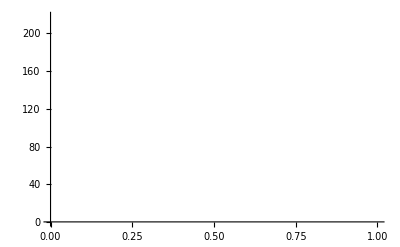

```mathematica
ListLinePlot[{mean,std}]
```

```mathematica
data=NormalizeData["QQQ",start,end];
daycount=20;
```

```mathematica
volatility=MovingMap[StandardDeviation,data,Quantity[daycount,"Events"]];
max0=MovingMap[Max,data,Quantity[daycount,"Events"]];
min0=MovingMap[Min,data,Quantity[daycount,"Events"]];
```

19

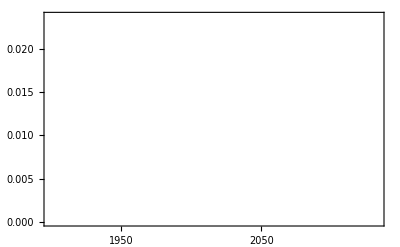

```mathematica
Length@data-Length@max0
DateListPlot[volatility]
```

```mathematica
max=Transpose[{Take[data[[All,1]],Length@max0],max0[[All,2]]}];
min=Transpose[{Take[data[[All,1]],Length@min0],min0[[All,2]]}];
```

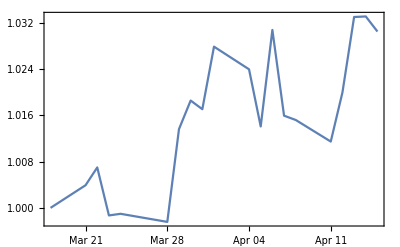

```mathematica
DateListPlot[{data,max,min}]
```

```mathematica
Last@max2
```

Last::normal: Nonatomic expression expected at position 1 in Last[max2].

Last[max2]

```mathematica
ListPlot[CorrelationFunction[max[[All,2]],{daycount}],Filling->Axis,PlotRange->All]
ListPlot[CorrelationFunction[min[[All,2]],{daycount}],Filling->Axis,PlotRange->All]
```

CorrelationFunction::bdlag: The lag specification {20} should be a symbol, an integer with magnitude less than the length of the data, or a range specification indicating such integers.

CorrelationFunction::bdlag: The lag specification {20.} should be a symbol, an integer with magnitude less than the length of the data, or a range specification indicating such integers.

General::stop: Further output of CorrelationFunction::bdlag will be suppressed during this calculation.

ListPlot::lpn: CorrelationFunction[{1.03306},{20.}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

ListPlot[CorrelationFunction[{1.03306},{20}],Filling→Axis,PlotRange→All]

CorrelationFunction::bdlag: The lag specification {20} should be a symbol, an integer with magnitude less than the length of the data, or a range specification indicating such integers.

CorrelationFunction::bdlag: The lag specification {20.} should be a symbol, an integer with magnitude less than the length of the data, or a range specification indicating such integers.

General::stop: Further output of CorrelationFunction::bdlag will be suppressed during this calculation.

ListPlot::lpn: CorrelationFunction[{0.997578},{20.}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

ListPlot[CorrelationFunction[{0.997578},{20}],Filling→Axis,PlotRange→All]

```mathematica
modelmax=TimeSeriesModelFit[max[[All,2]]];
modelmin=TimeSeriesModelFit[min[[All,2]]];
```

TimeSeriesModelFit::nmdlft: None of the candidate models could be successfully fitted to the data. Try a different model family or set of candidate models.

```mathematica
future=Range[Length@max+1,Length@max+daycount-1]
```

{2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
forecastmax=modelmax/@future;
forecastmin=modelmin/@future;
```

```mathematica
forecastmax//Length
```

19

```mathematica
forecastmax
```

{TimeSeriesModelFit[{1.03306}][2],TimeSeriesModelFit[{1.03306}][3],TimeSeriesModelFit[{1.03306}][4],TimeSeriesModelFit[{1.03306}][5],TimeSeriesModelFit[{1.03306}][6],TimeSeriesModelFit[{1.03306}][7],TimeSeriesModelFit[{1.03306}][8],TimeSeriesModelFit[{1.03306}][9],TimeSeriesModelFit[{1.03306}][10],TimeSeriesModelFit[{1.03306}][11],TimeSeriesModelFit[{1.03306}][12],TimeSeriesModelFit[{1.03306}][13],TimeSeriesModelFit[{1.03306}][14],TimeSeriesModelFit[{1.03306}][15],TimeSeriesModelFit[{1.03306}][16],TimeSeriesModelFit[{1.03306}][17],TimeSeriesModelFit[{1.03306}][18],TimeSeriesModelFit[{1.03306}][19],TimeSeriesModelFit[{1.03306}][20]}

```mathematica
lastday=First@Last@max;
futuredates=DateRange[DayPlus[lastday,1,"BusinessDay"],DayPlus[lastday,daycount-2,"BusinessDay"],"BusinessDay"]//DateList/@#&
```

{{2016,3,21,0,0,0.},{2016,3,22,0,0,0.},{2016,3,23,0,0,0.},{2016,3,24,0,0,0.},{2016,3,25,0,0,0.},{2016,3,28,0,0,0.},{2016,3,29,0,0,0.},{2016,3,30,0,0,0.},{2016,3,31,0,0,0.},{2016,4,1,0,0,0.},{2016,4,4,0,0,0.},{2016,4,5,0,0,0.},{2016,4,6,0,0,0.},{2016,4,7,0,0,0.},{2016,4,8,0,0,0.},{2016,4,11,0,0,0.},{2016,4,12,0,0,0.},{2016,4,13,0,0,0.}}

```mathematica
upper=TimeSeries[forecastmax,{futuredates}]
lower=TimeSeries[forecastmin,{futuredates}]
```

TemporalData::tpspc: The time specification {{{2016,3,21,0,0,0.},{2016,3,22,0,0,0.},{2016,3,23,0,0,0.},{2016,3,24,0,0,0.},{2016,3,25,0,0,0.},{2016,3,28,0,0,0.},{2016,3,29,0,0,0.},{2016,3,30,0,0,0.},{2016,3,31,0,0,0.},{2016,«5»},{2016,4,4,0,0,0.},{2016,4,5,0,0,0.},{2016,4,6,0,0,0.},{2016,4,7,0,0,0.},{2016,4,8,0,0,0.},{2016,4,11,0,0,0.},{2016,4,12,0,0,0.},{2016,4,13,0,0,0.}}} should be one of Automatic, a time range, a list containing a list of explicit times, or a list containing one such specification for each path in the data.

TimeSeries[{TimeSeriesModelFit[{1.03306}][2],TimeSeriesModelFit[{1.03306}][3],TimeSeriesModelFit[{1.03306}][4],TimeSeriesModelFit[{1.03306}][5],TimeSeriesModelFit[{1.03306}][6],TimeSeriesModelFit[{1.03306}][7],TimeSeriesModelFit[{1.03306}][8],TimeSeriesModelFit[{1.03306}][9],TimeSeriesModelFit[{1.03306}][10],TimeSeriesModelFit[{1.03306}][11],TimeSeriesModelFit[{1.03306}][12],TimeSeriesModelFit[{1.03306}][13],TimeSeriesModelFit[{1.03306}][14],TimeSeriesModelFit[{1.03306}][15],TimeSeriesModelFit[{1.03306}][16],TimeSeriesModelFit[{1.03306}][17],TimeSeriesModelFit[{1.03306}][18],TimeSeriesModelFit[{1.03306}][19],TimeSeriesModelFit[{1.03306}][20]},{{{2016,3,21,0,0,0.},{2016,3,22,0,0,0.},{2016,3,23,0,0,0.},{2016,3,24,0,0,0.},{2016,3,25,0,0,0.},{2016,3,28,0,0,0.},{2016,3,29,0,0,0.},{2016,3,30,0,0,0.},{2016,3,31,0,0,0.},{2016,4,1,0,0,0.},{2016,4,4,0,0,0.},{2016,4,5,0,0,0.},{2016,4,6,0,0,0.},{2016,4,7,0,0,0.},{2016,4,8,0,0,0.},{2016,4,11,0,0,0.},{2016,4,12,0,0,0.},{2016,4,13,0,0,0.}}}]

TemporalData::tpspc: The time specification {{{2016,3,21,0,0,0.},{2016,3,22,0,0,0.},{2016,3,23,0,0,0.},{2016,3,24,0,0,0.},{2016,3,25,0,0,0.},{2016,3,28,0,0,0.},{2016,3,29,0,0,0.},{2016,3,30,0,0,0.},{2016,3,31,0,0,0.},{2016,«5»},{2016,4,4,0,0,0.},{2016,4,5,0,0,0.},{2016,4,6,0,0,0.},{2016,4,7,0,0,0.},{2016,4,8,0,0,0.},{2016,4,11,0,0,0.},{2016,4,12,0,0,0.},{2016,4,13,0,0,0.}}} should be one of Automatic, a time range, a list containing a list of explicit times, or a list containing one such specification for each path in the data.

TimeSeries[{TimeSeriesModelFit[{0.997578}][2],TimeSeriesModelFit[{0.997578}][3],TimeSeriesModelFit[{0.997578}][4],TimeSeriesModelFit[{0.997578}][5],TimeSeriesModelFit[{0.997578}][6],TimeSeriesModelFit[{0.997578}][7],TimeSeriesModelFit[{0.997578}][8],TimeSeriesModelFit[{0.997578}][9],TimeSeriesModelFit[{0.997578}][10],TimeSeriesModelFit[{0.997578}][11],TimeSeriesModelFit[{0.997578}][12],TimeSeriesModelFit[{0.997578}][13],TimeSeriesModelFit[{0.997578}][14],TimeSeriesModelFit[{0.997578}][15],TimeSeriesModelFit[{0.997578}][16],TimeSeriesModelFit[{0.997578}][17],TimeSeriesModelFit[{0.997578}][18],TimeSeriesModelFit[{0.997578}][19],TimeSeriesModelFit[{0.997578}][20]},{{{2016,3,21,0,0,0.},{2016,3,22,0,0,0.},{2016,3,23,0,0,0.},{2016,3,24,0,0,0.},{2016,3,25,0,0,0.},{2016,3,28,0,0,0.},{2016,3,29,0,0,0.},{2016,3,30,0,0,0.},{2016,3,31,0,0,0.},{2016,4,1,0,0,0.},{2016,4,4,0,0,0.},{2016,4,5,0,0,0.},{2016,4,6,0,0,0.},{2016,4,7,0,0,0.},{2016,4,8,0,0,0.},{2016,4,11,0,0,0.},{2016,4,12,0,0,0.},{2016,4,13,0,0,0.}}}]

```mathematica
DateListPlot[{data,max,min,lower,upper},Joined->True,PlotTheme->"Detailed",Joined->True]
```

DateListPlot::ldata: {{{{2016,3,18},1.},{{2016,3,21},1.00391},{{2016,3,22},1.00699},{{2016,3,23},0.998696},{{2016,3,24},0.998975},«10»,{{2016,4,11},1.01146},{{2016,4,12},1.01993},{{2016,4,13},1.03297},{{2016,4,14},1.03306},{{2016,4,15},1.03046}},«3»,«1»} is not a valid dataset or list of datasets.

DateListPlot[{{{{2016,3,18},1.},{{2016,3,21},1.00391},{{2016,3,22},1.00699},{{2016,3,23},0.998696},{{2016,3,24},0.998975},{{2016,3,28},0.997578},{{2016,3,29},1.0136},{{2016,3,30},1.01853},{{2016,3,31},1.01704},{{2016,4,1},1.02785},{{2016,4,4},1.02394},{{2016,4,5},1.01406},{{2016,4,6},1.03073},{{2016,4,7},1.01593},{{2016,4,8},1.01518},{{2016,4,11},1.01146},{{2016,4,12},1.01993},{{2016,4,13},1.03297},{{2016,4,14},1.03306},{{2016,4,15},1.03046}},{{{2016,3,18},1.03306}},{{{2016,3,18},0.997578}},TimeSeries[{TimeSeriesModelFit[{0.997578}][2],TimeSeriesModelFit[{0.997578}][3],TimeSeriesModelFit[{0.997578}][4],TimeSeriesModelFit[{0.997578}][5],TimeSeriesModelFit[{0.997578}][6],TimeSeriesModelFit[{0.997578}][7],TimeSeriesModelFit[{0.997578}][8],TimeSeriesModelFit[{0.997578}][9],TimeSeriesModelFit[{0.997578}][10],TimeSeriesModelFit[{0.997578}][11],TimeSeriesModelFit[{0.997578}][12],TimeSeriesModelFit[{0.997578}][13],TimeSeriesModelFit[{0.997578}][14],TimeSeriesModelFit[{0.997578}][15],TimeSeriesModelFit[{0.997578}][16],TimeSeriesModelFit[{0.997578}][17],TimeSeriesModelFit[{0.997578}][18],TimeSeriesModelFit[{0.997578}][19],TimeSeriesModelFit[{0.997578}][20]},{{{2016,3,21,0,0,0.},{2016,3,22,0,0,0.},{2016,3,23,0,0,0.},{2016,3,24,0,0,0.},{2016,3,25,0,0,0.},{2016,3,28,0,0,0.},{2016,3,29,0,0,0.},{2016,3,30,0,0,0.},{2016,3,31,0,0,0.},{2016,4,1,0,0,0.},{2016,4,4,0,0,0.},{2016,4,5,0,0,0.},{2016,4,6,0,0,0.},{2016,4,7,0,0,0.},{2016,4,8,0,0,0.},{2016,4,11,0,0,0.},{2016,4,12,0,0,0.},{2016,4,13,0,0,0.}}}],TimeSeries[{TimeSeriesModelFit[{1.03306}][2],TimeSeriesModelFit[{1.03306}][3],TimeSeriesModelFit[{1.03306}][4],TimeSeriesModelFit[{1.03306}][5],TimeSeriesModelFit[{1.03306}][6],TimeSeriesModelFit[{1.03306}][7],TimeSeriesModelFit[{1.03306}][8],TimeSeriesModelFit[{1.03306}][9],TimeSeriesModelFit[{1.03306}][10],TimeSeriesModelFit[{1.03306}][11],TimeSeriesModelFit[{1.03306}][12],TimeSeriesModelFit[{1.03306}][13],TimeSeriesModelFit[{1.03306}][14],TimeSeriesModelFit[{1.03306}][15],TimeSeriesModelFit[{1.03306}][16],TimeSeriesModelFit[{1.03306}][17],TimeSeriesModelFit[{1.03306}][18],TimeSeriesModelFit[{1.03306}][19],TimeSeriesModelFit[{1.03306}][20]},{{{2016,3,21,0,0,0.},{2016,3,22,0,0,0.},{2016,3,23,0,0,0.},{2016,3,24,0,0,0.},{2016,3,25,0,0,0.},{2016,3,28,0,0,0.},{2016,3,29,0,0,0.},{2016,3,30,0,0,0.},{2016,3,31,0,0,0.},{2016,4,1,0,0,0.},{2016,4,4,0,0,0.},{2016,4,5,0,0,0.},{2016,4,6,0,0,0.},{2016,4,7,0,0,0.},{2016,4,8,0,0,0.},{2016,4,11,0,0,0.},{2016,4,12,0,0,0.},{2016,4,13,0,0,0.}}}]},Joined→True,PlotTheme→Detailed,Joined→True]

```mathematica
d=ExampleData[{"MachineLearning","BostonHomes"},"TrainingData"];
```

```mathematica
p=Predict[d,PerformanceGoal->"Quality"]
```

PredictorFunction[…]

```mathematica
d2=ExampleData[{"MachineLearning","BostonHomes"},"TestData"];
```

```mathematica
pm=PredictorMeasurements[p,d2]
```

PredictorMeasurementsObject[…]

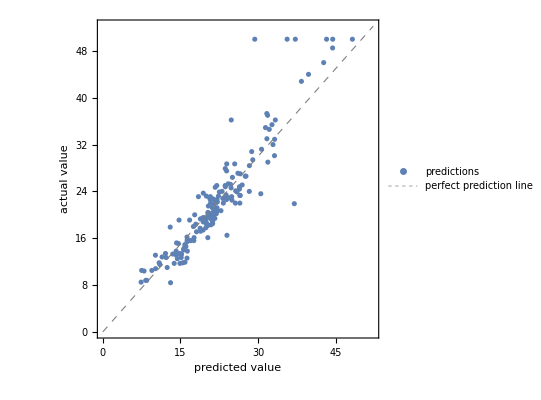

```mathematica
pm["ComparisonPlot"]
```

```mathematica
pm["StandardDeviation"]
```

3.53149